Using data from chapter2_holevo_comparisons.nb.
Goal: comparison of power of attacks BS0, BS1, BS2, EC. 
(i) which gives the best Holevo information?
	 - I should save until later to show best gsec and L, since I haven’t introduced them yet in my thesis.

```mathematica
<<MaTeX`
SetOptions[MaTeX,FontSize->12,Magnification->1,"DisplayStyle"->True]
style=Directive[FontFamily->"LM Roman 12",FontSize->10];
cm=72/2.54;
(* http://ksrowell.com/blog-visualizing-data/2012/02/02/optimal-colors-for-graphs/ *)
col1 = RGBColor[57/256, 106/256, 177/256]
col2 = RGBColor[218/256, 124/256, 48/256]
col3= RGBColor[62/256, 150/256, 81/256]
col4 = RGBColor[204/256, 37/256, 41/256]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

RGBColor[Rational[57, 256], Rational[53, 128], Rational[177, 256]]

RGBColor[Rational[109, 128], Rational[31, 64], Rational[3, 16]]

RGBColor[Rational[31, 128], Rational[75, 128], Rational[81, 256]]

RGBColor[Rational[51, 64], Rational[37, 256], Rational[41, 256]]

## “Importing” data

### Scanning alpha

```mathematica
(* dims=7, T=0.5 *)
bs0scanalpha1={{0.01,2.2749237282588403*^-8},{0.1,0.00012163267028315883},{0.2,0.0014376661250919687},{0.3,0.00578746608158015},{0.4,0.015019641338630818},{0.5,0.030682671763411995},{0.6,0.0539394356153603},{0.7,0.08557404288728776},{0.8,0.1259949444359395},{0.9,0.17517940778932473},{1.,0.23256151745943465},{1.1,0.296919573557868},{1.2,0.366341566793732},{1.3,0.4383313290483135},{1.4,0.5100655225194048},{1.5,0.5787441572565715},{1.6,0.6419174346389898},{1.7,0.6976546512323001}};
```

```mathematica
(* dims=7, T=0.5, barn=0.01 *)
bs1scanalpha1 = {{0.01,0.00011855994281288751},{0.1,1.3835671390516335*^-7},{0.2,0.0007645973184150223},{0.3,0.0044245510329680715},{0.4,0.012905820262269607},{0.5,0.02780092937295442},{0.6,0.05029686072005546},{0.7,0.08118695133746245},{0.8,0.12087943398875511},{0.9,0.16934760764891998},{1.,0.22601952383704416},{1.1,0.28965812259695145},{1.2,0.3583080948174464},{1.3,0.42937193599489665},{1.4,0.49982440077696877},{1.5,0.566509001623908},{1.6,0.6264149738230944},{1.7,0.6768468670803427}};
```

```mathematica
(* dims=7, T=0.5, barn=0.02 *)
bs1scanalpha2 = {{0.01,0.0004153038988137514},{0.1,0.00009529450406688122},{0.2,0.00032744724039257544},{0.3,0.0032935858343223767},{0.4,0.011015372622678099},{0.5,0.025134827882265953},{0.6,0.04686461913050033},{0.7,0.07700690511213726},{0.8,0.11596698017442275},{0.9,0.16371019668500475},{1.,0.21965996893027073},{1.1,0.2825851652089355},{1.2,0.35055095826314764},{1.3,0.42099426388064587},{1.4,0.49093307563288535},{1.5,0.5572532669128933},{1.6,0.6169728568588846},{1.7,0.6673988414266079}};
```

```mathematica
(* dims=8, T=0.5, barn=0.01 *)
ecscanalpha1 = {{0.01,0.02629037175439214-2.989976797305297*^-9 ⅈ},{0.1,0.02651725048485254-4.19621218411337*^-9 ⅈ},{0.2,0.028135407393922757-4.144306785152556*^-9 ⅈ},{0.3,0.03293902411533012-5.437642645762293*^-9 ⅈ},{0.4,0.04270742881500916-4.7792694157766785*^-9 ⅈ},{0.5,0.05889063480626722-5.520795903298151*^-9 ⅈ},{0.6,0.08253072110161741-5.081951563348499*^-9 ⅈ},{0.7,0.11429463056757228-5.6742101129048555*^-9 ⅈ},{0.8,0.15450858676773138-5.311525589975381*^-9 ⅈ},{0.9,0.20312094924661128-5.2716680979802426*^-9 ⅈ},{1.,0.2595901983888991-5.2491735773554595*^-9 ⅈ},{1.1,0.32275985838920596-4.653733195710639*^-9 ⅈ},{1.2,0.39080508240701506-4.997879418499504*^-9 ⅈ},{1.3,0.46131830652869343-4.591443565345746*^-9 ⅈ},{1.4,0.5315523726493949-4.5132555259987995*^-9 ⅈ},{1.5,0.5987701069100231-4.559080492866653*^-9 ⅈ},{1.6,0.6605774693365554-4.516329755195487*^-9 ⅈ},{1.7,0.715092440708452-4.479732902012567*^-9 ⅈ}};
```

```mathematica
(* dims=8 T=0.5, barn=0.02 *)
ecscanalpha2 = {{0.01,0.04625118562745688-5.902145142257499*^-9 ⅈ},{0.1,0.046551644646262214-5.627883368728528*^-9 ⅈ},{0.2,0.04837858230627509-6.794829135817515*^-9 ⅈ},{0.3,0.053490655215816696-7.629999409546861*^-9 ⅈ},{0.4,0.0636207349086178-7.576077159811775*^-9 ⅈ},{0.5,0.08016316936277901-7.088407633422001*^-9 ⅈ},{0.6,0.10409330178902865-6.534055405335867*^-9 ⅈ},{0.7,0.13600198639177286-6.305609407400424*^-9 ⅈ},{0.8,0.1761428542212914-5.985033206846667*^-9 ⅈ},{0.9,0.22441426320341984-5.806108560380053*^-9 ⅈ},{1.,0.28026174491848654-6.149416687154884*^-9 ⅈ},{1.1,0.34255561486267516-6.767072668185661*^-9 ⅈ},{1.2,0.40953077860353626-6.58691204864179*^-9 ⅈ},{1.3,0.4788589518334414-5.459812430567269*^-9 ⅈ},{1.4,0.5478732297137605-6.008831949012503*^-9 ⅈ},{1.5,0.6138996219624229-6.697140430625315*^-9 ⅈ},{1.6,0.6745805378793663-6.650186627249618*^-9 ⅈ},{1.7,0.7280420390544942-5.804139782862709*^-9 ⅈ}};
```

### Scanning T

```mathematica
(* dims=7, alpha=0.5 *)
bs0scanT1 = {{0.01,0.000992521916241773},{0.1,0.009278445157728799},{0.2,0.017079279567124295},{0.3,0.02332406623836747},{0.4,0.027907191790648378},{0.5,0.030682671763411995},{0.6,0.03144091515920783},{0.7,0.02986305174335685},{0.8,0.02541453980502928},{0.9,0.017010145802629356},{0.99,0.0029404693194066515}};
```

```mathematica
(* dims=7, alpha=0.5, barn=0.01 *)
bs1scanT1 = {{0.01,0.0009148501507987294},{0.1,0.008532653266361212},{0.2,0.015662249547896745},{0.3,0.021319616562359922},{0.4,0.02540992722419011},{0.5,0.02780092937295442},{0.6,0.028302255778397067},{0.7,0.02662532058132472},{0.8,0.022292453042370153},{0.9,0.014368700533450574},{0.99,0.001977833981019264}};
```

```mathematica
(* dims=7, alpha=0.5, barn=0.02 *)
bs1scanT2 = {{0.01,0.0008418200311821611},{0.1,0.007831274567385749},{0.2,0.014331520926741614},{0.3,0.019442716325919318},{0.4,0.023082576904389085},{0.5,0.025134827882265953},{0.6,0.025431878197600344},{0.7,0.023722076664408565},{0.8,0.01959904347816721},{0.9,0.012312505148681763},{0.99,0.001581372061060654}};
```

```mathematica
(* dims=8, alpha=0.5, barn=0.01 *)
ecscanT1 = {{0.01,0.046902594163226285-3.2108454349662522*^-9 ⅈ},{0.1,0.05212340565249707-3.875563392379451*^-9 ⅈ},{0.2,0.05646801753070463-3.753469563882084*^-9 ⅈ},{0.3,0.05915919597234598-3.941609795463467*^-9 ⅈ},{0.4,0.060037279397672005-5.347246414956914*^-9 ⅈ},{0.5,0.05889063480626722-5.520795903298151*^-9 ⅈ},{0.6,0.0554270412309536-5.781651924444026*^-9 ⅈ},{0.7,0.04921744444769799-5.6622643081247164*^-9 ⅈ},{0.8,0.03956500832400278-6.31060239546055*^-9 ⅈ},{0.9,0.02509156867387738-5.827752240433184*^-9 ⅈ},{0.99,0.004046729487028847-3.3200756048855936*^-9 ⅈ}};
```

```mathematica
(* dims=8, alpha=0.5, barn=0.01 *)
ecscanT2 = {{0.01,0.08033474055898815-3.106740075477281*^-9 ⅈ},{0.1,0.083482746659017-4.680109260048508*^-9 ⅈ},{0.2,0.08547651551968583-6.231780939838466*^-9 ⅈ},{0.3,0.08573286511634137-6.175205518034864*^-9 ⅈ},{0.4,0.08404993382766579-6.8817760100333614*^-9 ⅈ},{0.5,0.08016316936277901-7.088407633422001*^-9 ⅈ},{0.6,0.07371118915099745-7.695959817626098*^-9 ⅈ},{0.7,0.0641685565067544-7.248983688216057*^-9 ⅈ},{0.8,0.050689337778944465-6.343295571895497*^-9 ⅈ},{0.9,0.03161339000195404-6.204639078485069*^-9 ⅈ},{0.99,0.0049932028804366875-3.657979458635327*^-9 ⅈ}};
```

### Scanning barn

```mathematica
(* dims=6, alpha=0.5, T=0.5 *)
bs1scanbarn1 = {{0.001,0.03038894256418201},{0.002,0.030092702835897822},{0.003,0.029798788253465158},{0.004,0.02950717121773927},{0.005,0.02921782868039502},{0.006,0.028930739352039492},{0.007,0.028645882963196923},{0.008,0.028363239973400955},{0.009,0.028082791419557718},{0.01,0.027804518828843494},{0.015,0.026445176976402585},{0.02,0.025137675312684182},{0.025,0.02388006734544945},{0.03,0.022670552899336283}};
```

```mathematica
(* dims=6, alpha=0.5, T=0.8 *)
bs1scanbarn2 = {{0.001,0.02508644235744123},{0.002,0.024756797653048446},{0.003,0.024432472608587885},{0.004,0.02411330431281694},{0.005,0.023799140419479448},{0.006,0.02348983763680279},{0.007,0.02318526057679121},{0.008,0.02288528092435088},{0.009,0.022589776772416692},{0.01,0.02229863207031285},{0.015,0.02090459426438035},{0.02,0.019604825437265105},{0.025,0.0183893931674165},{0.03,0.017250061058286248}};
```

```mathematica
(* dims=6, alpha=0.5, T=0.2 *)
bs1scanbarn3 = {{0.001,0.01693596833593214},{0.002,0.016791078543586968},{0.003,0.016647095850801708},{0.004,0.016504009513919615},{0.005,0.016361813168136452},{0.006,0.01622050173775147},{0.007,0.016080070805317925},{0.008,0.01594051623621262},{0.009,0.015801834146412452},{0.01,0.015664020725593475},{0.015,0.014987856423219204},{0.02,0.01433287629753699},{0.025,0.01369865918902402},{0.03,0.013084798982012202}};
```

```mathematica
(* dims=8, alpha=0.5, T=0.5 *)
ecscanbarn1 = {{0.001,0.03463615532120745-2.5554585253264006*^-9 ⅈ},{0.002,0.037917302216292526-3.377969484704134*^-9 ⅈ},{0.003,0.04093800605217901-3.304404841691123*^-9 ⅈ},{0.004,0.04378864727459908-4.229285954829451*^-9 ⅈ},{0.005,0.046512496421244554-4.692489836372153*^-9 ⅈ},{0.006,0.04913516556423103-4.449434015944581*^-9 ⅈ},{0.007,0.05167363979309669-5.508880917069173*^-9 ⅈ},{0.008,0.05414000133933339-4.83900190785161*^-9 ⅈ},{0.009,0.05654331869512397-5.739413776758144*^-9 ⅈ},{0.01,0.05889063480626722-5.520795903298151*^-9 ⅈ},{0.015,0.06995322443170227-5.907267808503568*^-9 ⅈ},{0.02,0.08016316936277901-7.088407633422001*^-9 ⅈ},{0.025,0.0897410150913952-6.9205789194966*^-9 ⅈ},{0.03,0.09881685178059807-6.6923705302580785*^-9 ⅈ}};
```

```mathematica
(* dims=8, alpha=0.5, T=0.8 *)
ecscanbarn2 = {{0.001,0.027326856108643383-1.9013516967206536*^-9 ⅈ},{0.002,0.02894271546311139-3.294552192818353*^-9 ⅈ},{0.003,0.03044446944543383-2.827503285450707*^-9 ⅈ},{0.004,0.03187197323066049-4.159792247722301*^-9 ⅈ},{0.005,0.03324420370971626-5.224521524465771*^-9 ⅈ},{0.006,0.034572363934387285-4.526072902121229*^-9 ⅈ},{0.007,0.03586387836888194-5.0617009832443614*^-9 ⅈ},{0.008,0.037124000727937034-5.236831699886509*^-9 ⅈ},{0.009,0.038356692634713474-5.9605212818249965*^-9 ⅈ},{0.01,0.03956500832400278-6.31060239546055*^-9 ⅈ},{0.015,0.04531306543448427-6.434601861097188*^-9 ⅈ},{0.02,0.050689337778944465-6.343295571895497*^-9 ⅈ},{0.025,0.055789346521604-7.50894725892345*^-9 ⅈ},{0.03,0.06066939835295404-7.903143200298871*^-9 ⅈ}};
```

```mathematica
(* dims=8, alpha=0.5, T=0.2 *)
ecscanbarn3 = {{0.001,0.022734851556020508-1.8361649620361789*^-9 ⅈ},{0.002,0.02736252988647514-1.887331280903742*^-9 ⅈ},{0.003,0.031598222139888166-2.3362490049404948*^-9 ⅈ},{0.004,0.03557876958193984-3.013558402990707*^-9 ⅈ},{0.005,0.03936941534131977-2.6994071009420117*^-9 ⅈ},{0.006,0.04300871741297685-3.5114872546256554*^-9 ⅈ},{0.007,0.04652220203481661-3.985354040260641*^-9 ⅈ},{0.008,0.0499280177890431-4.771318018177133*^-9 ⅈ},{0.009,0.05323977290771065-4.4718517302966275*^-9 ⅈ},{0.01,0.05646801753070463-3.753469563882084*^-9 ⅈ},{0.015,0.07160576275465935-5.3418401150868656*^-9 ⅈ},{0.02,0.08547651551968583-6.231780939838466*^-9 ⅈ},{0.025,0.09841051159891456-6.0463623540107*^-9 ⅈ},{0.03,0.11060243002093706-7.012100014585966*^-9 ⅈ}};
```

## Making some graphs

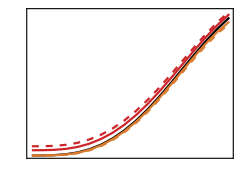

```mathematica
fs1=15;
fs2=10;
fig1= ListPlot[
{
bs0scanalpha1,
bs1scanalpha1,
bs1scanalpha2,
ecscanalpha1//Re,
ecscanalpha2//Re
},
PlotStyle->{{Black}, {col2}, {col2, Dashed}, {col4}, {col4, Dashed}},
Joined->True,
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
ImageSize->8.6cm,
AspectRatio->1/1.4,
FrameLabel->{MaTeX["\\text{Amplitude } \\alpha", ContentPadding->False, FontSize->fs1],
MaTeX["\\text{Holevo } \\chi", ContentPadding->False,
FontSize->fs1]
},
FrameTicks->{{{{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]}, {0.35, MaTeX["0.35", ContentPadding->False, FontSize->fs2]}, {0.7, MaTeX["0.7", ContentPadding->False, FontSize->fs2]}}, None},
{{{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]}, {0.5, MaTeX["0.5", ContentPadding->False, FontSize->fs2]}, {1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]}, 
{1.5, MaTeX["1.5", ContentPadding->False, FontSize->fs2]}}, None}}
];
fig1~Magnify~2
```

```mathematica
Export[NotebookDirectory[]<>"\\"<>"holveo_comparisons_varalpha.pdf", fig1]
```

C:\Users\MatthewThornton\OneDrive for Business\Thesis\Writing\Images\qds\\holveo_comparisons_varalpha.pdf

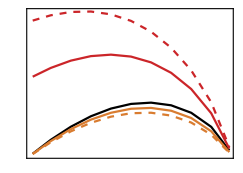

```mathematica
fig2 = ListPlot[
{
bs0scanT1,
bs1scanT1,
bs1scanT2,
ecscanT1//Re,
ecscanT2//Re
},
PlotStyle->{{Black}, {col2}, {col2, Dashed}, {col4}, {col4, Dashed}},
Joined->True,
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
ImageSize->8.6cm,
AspectRatio->1/1.4,
FrameLabel->{MaTeX["\\text{Transmission } T", ContentPadding->False, FontSize->fs1],
MaTeX["\\text{Holevo } \\chi", ContentPadding->False,
FontSize->fs1]
},
FrameTicks->{{{{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]}, {0.02, MaTeX["0.02", ContentPadding->False, FontSize->fs2]}, {0.04, MaTeX["0.04", ContentPadding->False, FontSize->fs2]},
{0.06, MaTeX["0.06", ContentPadding->False, FontSize->fs2]},
{0.08, MaTeX["0.08", ContentPadding->False, FontSize->fs2]}


}, None},
{{{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]}, {0.2, MaTeX["0.2", ContentPadding->False, FontSize->fs2]}, {0.4,  MaTeX["0.4", ContentPadding->False, FontSize->fs2]}, 
{0.6, MaTeX["0.6", ContentPadding->False, FontSize->fs2]},
{0.8, MaTeX["0.8", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]}
}, None}}
];
fig2~Magnify~2
```

```mathematica
Export[NotebookDirectory[]<>"\\"<>"holveo_comparisons_varT.pdf", fig2]
```

C:\Users\MatthewThornton\OneDrive for Business\Thesis\Writing\Images\qds\\holveo_comparisons_varT.pdf

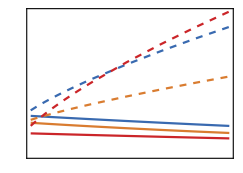

```mathematica
fig3 = ListPlot[
{
bs1scanbarn1,
bs1scanbarn2,
bs1scanbarn3,
ecscanbarn1//Re,
ecscanbarn2//Re,
ecscanbarn3//Re
},
PlotStyle->{col1, col2, col4, {col1, Dashed}, {col2, Dashed}, {col4, Dashed}},
Joined->True,
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
ImageSize->8.6cm,
AspectRatio->1/1.4,
FrameLabel->{MaTeX["\\text{Thermal photons } \\bar{n}", ContentPadding->False, FontSize->fs1],
MaTeX["\\text{Holevo } \\chi", ContentPadding->False,
FontSize->fs1]
},
FrameTicks->{{{{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]}, {0.02, MaTeX["0.02", ContentPadding->False, FontSize->fs2]}, {0.04, MaTeX["0.04", ContentPadding->False, FontSize->fs2]},
{0.06, MaTeX["0.06", ContentPadding->False, FontSize->fs2]},
{0.08, MaTeX["0.08", ContentPadding->False, FontSize->fs2]},
{0.1, MaTeX["0.10", ContentPadding->False, FontSize->fs2]}


}, None},
{{{0.001, MaTeX["0.001", ContentPadding->False, FontSize->fs2]}, {0.01, MaTeX["0.01", ContentPadding->False, FontSize->fs2]}, {0.02,  MaTeX["0.02", ContentPadding->False, FontSize->fs2]}, 
{0.03, MaTeX["0.03", ContentPadding->False, FontSize->fs2]},
{0.8, MaTeX["0.8", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]}
}, None}},
PlotRange->{{0.001, 0.03}, All}
];
fig3~Magnify~2
```

```mathematica
Export[NotebookDirectory[]<>"\\"<>"holveo_comparisons_varbarn.pdf", fig3]
```

C:\Users\MatthewThornton\OneDrive for Business\Thesis\Writing\Images\qds\\holveo_comparisons_varbarn.pdf